```mathematica
importList={"KP01_Dataset.xlsx","KP02_Dataset.xlsx","KP03_Dataset.xlsx","KP04_Dataset.xlsx","KP05_Dataset.xlsx","KP06_Dataset.xlsx","KP07_Dataset.xlsx","KP08_Dataset.xlsx","KP09_Dataset.xlsx","KP10_Dataset.xlsx","KP11_Dataset.xlsx","KP12_Dataset.xlsx","Kl02_Dataset.xlsx","Ob02_Dataset.xlsx","Ob03_Dataset.xlsx","Ob04_Dataset.xlsx","Ob05_Dataset.xlsx","Ob06_Dataset.xlsx","Ob07_Dataset.xlsx","Ob08_Dataset.xlsx","Ob09_Dataset.xlsx","Ob10_Dataset.xlsx","Ob11_Dataset.xlsx","Ob12_Dataset.xlsx","Qu01_Dataset.xlsx","Qu02_Dataset.xlsx","Qu03_Dataset.xlsx","Qu04_Dataset.xlsx","Qu05_Dataset.xlsx","Qu06_Dataset.xlsx","Qu07_Dataset.xlsx","Qu09_Dataset.xlsx","Qu10_Dataset.xlsx","Qu11_Dataset.xlsx","Qu12_Dataset.xlsx","Qu13_Dataset.xlsx","Qu14_Dataset.xlsx","Qu15_Dataset.xlsx","Qu16_Dataset.xlsx","Qu17_Dataset.xlsx","Qu18_Dataset.xlsx","Qu19_Dataset.xlsx","Qu20_Dataset.xlsx","Tr01_Dataset.xlsx"}
```

{KP01_Dataset.xlsx,KP02_Dataset.xlsx,KP03_Dataset.xlsx,KP04_Dataset.xlsx,KP05_Dataset.xlsx,KP06_Dataset.xlsx,KP07_Dataset.xlsx,KP08_Dataset.xlsx,KP09_Dataset.xlsx,KP10_Dataset.xlsx,KP11_Dataset.xlsx,KP12_Dataset.xlsx,Kl02_Dataset.xlsx,Ob02_Dataset.xlsx,Ob03_Dataset.xlsx,Ob04_Dataset.xlsx,Ob05_Dataset.xlsx,Ob06_Dataset.xlsx,Ob07_Dataset.xlsx,Ob08_Dataset.xlsx,Ob09_Dataset.xlsx,Ob10_Dataset.xlsx,Ob11_Dataset.xlsx,Ob12_Dataset.xlsx,Qu01_Dataset.xlsx,Qu02_Dataset.xlsx,Qu03_Dataset.xlsx,Qu04_Dataset.xlsx,Qu05_Dataset.xlsx,Qu06_Dataset.xlsx,Qu07_Dataset.xlsx,Qu09_Dataset.xlsx,Qu10_Dataset.xlsx,Qu11_Dataset.xlsx,Qu12_Dataset.xlsx,Qu13_Dataset.xlsx,Qu14_Dataset.xlsx,Qu15_Dataset.xlsx,Qu16_Dataset.xlsx,Qu17_Dataset.xlsx,Qu18_Dataset.xlsx,Qu19_Dataset.xlsx,Qu20_Dataset.xlsx,Tr01_Dataset.xlsx}

```mathematica
dRoomConditions={};
```

```mathematica
AppendTo[dRoomConditions,Import["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-wind-instruments/datasets/"<>#,{"Sheets","Zeitleiste"}]]&/@importList;
```

```mathematica
tempNoTask=.
tempNoTask[l_]:=Select[l,(#[[7]]!=1&&#[[8]]!=1&&#[[9]]!=1&&#[[10]]!=1&&#[[11]]!=1)&]
selectRoomCond=.
selectRoomCond[l_]:=Select[l[[All,#]], NumberQ]&/@{4,5,6}
thermoHygroBaro=selectRoomCond[tempNoTask[#]]&/@dRoomConditions
```

## Temperature

```mathematica
stats=.
stats[v_]:={Min[v],Mean[v], StandardDeviation[v],Median[v],Max[v],Histogram[v], FindDistribution[v, TargetFunctions->{NormalDistribution}]}
```

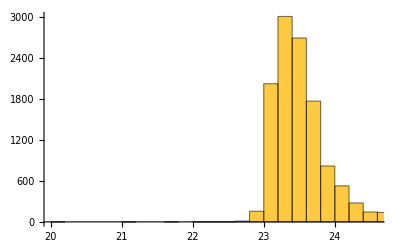
{20.1,23.4481,0.355615,23.4,25.3,-Graphics-,MixtureDistribution[{0.961041,0.0389587},{NormalDistribution[23.4222,0.30258],NormalDistribution[23.756,1.27033]}]}

```mathematica
stats[Flatten[thermoHygroBaro[[All,1]]]]
```

## Humidity

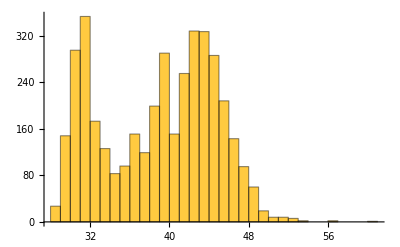
{28.,38.837,5.73519,39.6,60.4,-Graphics-,MixtureDistribution[{0.215681,0.362733,0.421586},{NormalDistribution[30.8668,0.871953],NormalDistribution[38.6172,5.21671],NormalDistribution[43.3084,2.35107]}]}

```mathematica
stats[Flatten[thermoHygroBaro[[All,2]]]]
```

## Air Pressure

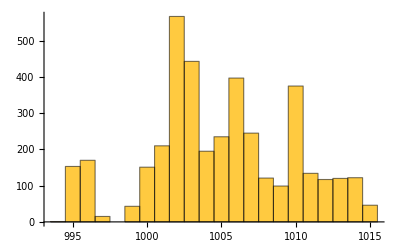
{994.,1004.96,4.82229,1005.,1015.,-Graphics-,MixtureDistribution[{0.119131,0.381959,0.201278,0.297632},{NormalDistribution[995.707,0.688192],NormalDistribution[1002.03,1.23147],NormalDistribution[1006.02,0.771048],NormalDistribution[1010.89,2.25486]}]}

```mathematica
stats[Flatten[thermoHygroBaro[[All,3]]]]
```

## Air flow

```mathematica
anemometer=Select[#,(#[[8]]==1||#[[9]]==1||#[[11]]==1)&][[All,3]]&/@dRoomConditions
```

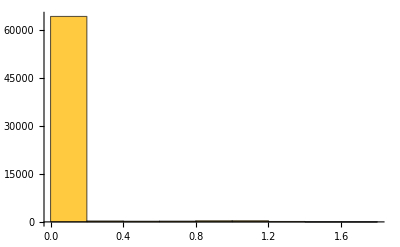
{0.,0.0194681,0.130782,0.,1.62,-Graphics-,NormalDistribution[0.0194894,0.130799]}

```mathematica
stats[dAnemo=Select[Flatten[anemometer],NumberQ]]
```

```mathematica
Sort[Select[Mean@Select[#,NumberQ] &/@anemometer,NumberQ]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,5.50661×10^-6,5.54939×10^-6,8.29187×10^-6,8.3682×10^-6,0.0000407747,0.245628,0.334785}